# Two strain dengue with vaccination

by   R. Adenane, F. Avram and A.D. Halanay

ABSTRACT (original article): 
Keywords: 

 CITATION (original article):

```mathematica
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[La]:=Λ;Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];Format[alv]:=Subscript[α,v];
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[y1]:=Subscript[y,1];Format[y2]:=Subscript[y,2];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];
Format[c1]:=Subscript[c,1];Format[c2]:=Subscript[c,2];
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];Needs["ReactionKinetics`"];
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "EpidCRNmodels"}]];<<EpidCRN`;(*Names["EpidCRN`*"]*)
```

```mathematica
(*enter closed model, as first step*)
cDFEm={i1->0,i2->0,y1->0,y2->0};cDFEM={i1->0,i2->0,y1->0,y2->0,c1->0,c2->0,r1->0,r2->0};
cE2={i1->0,y1->0};cE1={i2->0,y2->0};
cACR={v ->xi mu/(mu+thv)};
ctr={c1->i1 ga1 /(mu+th1),c2->i2 ga2 /(mu+th2),v ->xi mu/(mu+thv)};
cd={d1->ga1 /(mu+th1),d2->ga2 /(mu+th2)};
sd=1-xi;vd=xi mu/(mu+thv);zd=xi thv/(mu+thv);mR1=be1/(ga1+mu);mR2=be2/(ga2+mu);
R1=mR1 sd;R2=mR2 (sd +alv zd);s2=1/mR2;s1=1/mR1;
k1=ga1/(ga1+mu+t1);a2c=1/k1;R12=mR2 (s1+ si2 r11);r11=k1(sd-s1);
R2c=R2/R12;
```

nR=17

Bulhosa closed(1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | -1 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

has rank 11  deficiency δ=N-L-S=27-10-11=6 and 1 cons cons[{{1,-1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{-1,0,0,0,-1,0,0,0,-1,-1,0,0,0,0,0,0,0},{0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,1,0,0,1,1,-1,0},{0,0,0,0,1,-1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,-1,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,-1,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}]

12 variables={c_I1,c_S,c_C1,c_R1,c_Y2,c_I2,c_C2,c_R2,c_Y1,c_V,c_Z,c_R}={i_1,s,c_1,r_1,y_2,i_2,c_2,r_2,y_1,v,z,r}12

rates

{β_1,γ_1,θ_1,α_2 β_2,β_2,γ_2,θ_2,α_1 β_1,β_1,β_2,α_2 β_2,α_1 β_1,θ_v,α_v β_2,α_v β_2,γ_2,γ_1}

Bulh RHS:(k[1]-x1 x2 k[2]-x1 x3 k[3]
x1 x2 k[2]-x2 x3 k[4]-x2 k[5]
x1 x3 k[3]-x2 x3 k[4]-x3 k[6]
x2 x3 k[4]-x4 k[7]) has Rv= Transpose[Rv]

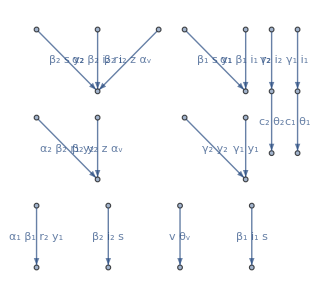

```mathematica
RNc={"S"+"I1"->2  "I1", "I1"-> "C1", "C1"-> "R1", "R1"+  "Y2"->2  "Y2",
"S"+"I2" ->2  "I2", "I2"-> "C2", "C2"-> "R2", "R2"+ "Y1"->2"Y1",
"S"+"Y1" ->  "Y1"+  "I1","S"+"Y2" ->  "Y2"+ "I2",
 "R1"+  "I2"-> "I2"+  "Y2", "R2"+"I1"->"I1"+"Y1","V"->"Z","Z"+"Y2"-> 2"Y2",
 "Z"+ "I2"->  "I2"+  "Y2", "Y2"->"R", "Y1"->"R"};
var={i1,s,c1,r1,y2,i2,c2,r2,y1,v,z,r};
RNDc=ReactionsData[RNc];
Γc= RNDc["γ"]//Normal;con=cons[Γc];
expoc= RNDc["α"]//Normal//Transpose;Print["nR=",nRc=RNDc["R"]]
{nS,defic,comc}=
RNDc["M","deficiency","complexes"];

Print["Bulhosa closed",Γc//MatrixForm]
Print["has rank ",MatrixRank[Γc],
"  deficiency ", defic, " and ",con//Length," cons ",con(*x=con.var*)]
Print[RNDc["variables"]//Length," variables=",RNDc["variables"],"=",var,var//Length]
monoc=expM[var,expoc];
Print["constants"];
tkc={be1,ga1,th1,al2 be2,be2,ga2,th2,al1 be1,be1,be2,al2 be2,al1 be1,thv,alv be2,alv be2,
ga2,ga1}
cpc=Thread[tkc>0];Rvc=tkc* monoc;
cv=Thread[var>=0];ctc=Join[cpc,cv];RHSc=Γc.Rvc//Simplify;
Print["Bulh RHS:",RHS//MatrixForm," has Rv= ",Rv//Transpose//MatrixForm]
ShowFHJGraph[RNc,Rvc,DirectedEdges->True,VertexLabeling->True,ImageSize->330]
```

nR=31

Bulhosa SM(1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

has rank 12  deficiency δ=N-L-S=29-7-12=10 and 1 cons cons[{{1,-1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,1,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,1,0,0,1,1,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,1,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,1,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}]

12 variables={c_I1,c_S,c_C1,c_R1,c_Y2,c_I2,c_C2,c_R2,c_Y1,c_V,c_Z,c_R}={i_1,s,c_1,r_1,y_2,i_2,c_2,r_2,y_1,v,z,r}12

Bulh RHS with lin. elim:(-i_1 (γ_1+μ-β_1 s)+β_1 s y_1
-μ (-1+s+ξ)-s (β_1 (i_1+y_1)+β_2 (i_2+y_2))
0
(γ_1 i_1 θ_1)/(μ+θ_1)-r_1 (μ+α_2 β_2 (i_2+y_2))
-((γ_2+μ) y_2)+β_2 (i_2+y_2) (α_2 r_1+α_v z)
-i_2 (γ_2+μ-β_2 s)+β_2 s y_2
0
(γ_2 i_2 θ_2)/(μ+θ_2)-r_2 (μ+α_1 β_1 (i_1+y_1))
-((γ_1+μ) y_1)+α_1 β_1 r_2 (i_1+y_1)
0
(μ θ_v ξ)/(μ+θ_v)-(μ+α_v β_2 (i_2+y_2)) z) has Rv= (β_1 i_1 s
γ_1 i_1
c_1 θ_1
α_2 β_2 r_1 y_2
β_2 i_2 s
γ_2 i_2
c_2 θ_2
α_1 β_1 r_2 y_1
β_1 s y_1
β_2 s y_2
α_2 β_2 i_2 r_1
α_1 β_1 i_1 r_2
θ_v v
α_v β_2 y_2 z
α_v β_2 i_2 z
γ_2 y_2
γ_1 y_1
μ (1-ξ)
μ ξ
μ s
i_1 μ
c_1 μ
μ r_1
μ y_2
i_2 μ
c_2 μ
μ r_2
μ y_1
μ v
μ z
μ r)

Check sum -μ (-1+c_1+c_2+i_1+i_2+r+r_1+r_2+s+v+y_1+y_2+z) reveals N=La/mu is conserved

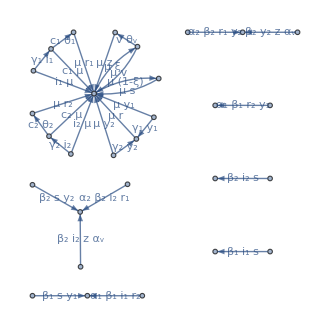

{i , s, c , r , y , i , c , r , y , v, z, r}
  1      1   1   2   2   2   2   1

minSiph[{i , s, c , r , y , i , c , r , y , v, z, r}
  1      1   1   2   2   2   2   1,{<|Substrates→{I1,S},Products→{I1}|>,<|Substrates→{I1},Products→{C1}|>,<|Substrates→{C1},Products→{R1}|>,<|Substrates→{R1,Y2},Products→{Y2}|>,<|Substrates→{I2,S},Products→{I2}|>,<|Substrates→{I2},Products→{C2}|>,<|Substrates→{C2},Products→{R2}|>,<|Substrates→{R2,Y1},Products→{Y1}|>,<|Substrates→{S,Y1},Products→{I1,Y1}|>,<|Substrates→{S,Y2},Products→{I2,Y2}|>,<|Substrates→{I2,R1},Products→{I2,Y2}|>,<|Substrates→{I1,R2},Products→{I1,Y1}|>,<|Substrates→{V},Products→{Z}|>,<|Substrates→{Y2,Z},Products→{Y2}|>,<|Substrates→{I2,Z},Products→{I2,Y2}|>,<|Substrates→{Y2},Products→{R}|>,<|Substrates→{Y1},Products→{R}|>,<|Substrates→{},Products→{S}|>,<|Substrates→{},Products→{V}|>,<|Substrates→{S},Products→{}|>,<|Substrates→{I1},Products→{}|>,<|Substrates→{C1},Products→{}|>,<|Substrates→{R1},Products→{}|>,<|Substrates→{Y2},Products→{}|>,<|Substrates→{I2},Products→{}|>,<|Substrates→{C2},Products→{}|>,<|Substrates→{R2},Products→{}|>,<|Substrates→{Y1},Products→{}|>,<|Substrates→{V},Products→{}|>,<|Substrates→{Z},Products→{}|>,<|Substrates→{R},Products→{}|>}]

```mathematica
(*enter open model, adding in and out  reactions; jac *)
RN=Join[RNc,{0->"S",0->"V",
"S"->0,"I1" ->0,"C1" ->0,"R1" ->0,"Y2" ->0,"I2" ->0,"C2" ->0,"R2" ->0,"Y1" ->0,"V"->0,"Z"->0,"R"->0}];
var={i1,s,c1,r1,y2,i2,c2,r2,y1,v,z,r};RND=ReactionsData[RN];
Γ= RND["γ"]//Normal;con=cons[Γ];
expo= RND["α"]//Normal//Transpose;Print["nR=",nR=RND["R"]]
{nS,defi,com}=
RND["M","deficiency","complexes"];
Print["Bulhosa SM",Γ//MatrixForm]
Print["has rank ",MatrixRank[Γ],
"  deficiency ", RND["deficiency"], " and ",con//Length," cons ",con(*x=con.var*)]

Print[RND["variables"]//Length," variables=",RND["variables"],"=",var,var//Length]
 mono=expM[var,expo];(*{ xA xB, xB xC, xC,  xD,xE};*)
tk={ be1,ga1,th1,al2 be2,be2,ga2,th2,al1 be1,be1,be2,al2 be2,al1 be1,
thv,alv be2,alv be2,ga2,ga1,(1- xi) mu,xi mu,mu,mu,mu,
mu,mu,mu,mu,mu,mu,mu,mu,mu};par=Variables[tk];
cp=Thread[par>0];
Rv=tk* mono;
cv=Thread[var>=0];ct=Join[cp,cv];
RHS=Γ.Rv//Simplify;
RHSl=Drop[RHS/.ctr,-1];
Print["Bulh RHS with lin. elim:",RHSl//FullSimplify//MatrixForm," has Rv= ",Rv//Transpose//MatrixForm]
Print["Check sum ",Total[RHS]//FullSimplify," reveals N=La/mu is conserved"]
ShowFHJGraph[RN,Rv,DirectedEdges->True,VertexLabeling->True,ImageSize->330]
spe=ToString[var]
minSiph[spe,asoRea[RN]]
```

```mathematica
(*Solve DFE and E1, E2 boundary, jac*)
jac=Grad[(RHS),var];
(*ch=CharacteristicPolynomial[jac,u]//Factor*)
ch=CharacteristicPolynomial[(jac/.cDFEm),u]//Factor;
Print["multistr with ch="]
ch
eqs=Thread[RHS==0];eqs//MatrixForm
so=Solve[(eqs//.cDFEm),var]//Factor;
so=Solve[(eqs//.Join[cE1,ctr]),var]//Factor;
Print["at E1 we have ",so//Length," fps ",so]

eq2=(eqs//.Join[cE2,ctr]);

vars=Delete[var,2];
Print["at E2 it holds "]
Timing[so=Solve[Delete[eq2,2],vars]//FullSimplify]
nu=eq2[[2]]/.so
nu1=nu[[1]][[1]]/.s->La(1-xi)/(x+mu)
co=CoefficientList[Numerator[Together[nu1]]/(mu(1-xi))//Factor,x]//FullSimplify
```

multistr with ch=

(μ+u)^5 (γ_1+μ+u) (γ_2+μ+u) (γ_1+μ-α_1 β_1 r_2-β_1 s+u) (μ+θ_1+u) (μ+θ_2+u) (μ+θ_v+u) (γ_2+μ-α_2 β_2 r_1-β_2 s+u-α_v β_2 z)

(-γ_1 i_1-i_1 μ+β_1 i_1 s+β_1 s y_1==0
-μ (-1+s+ξ)-s (β_1 (i_1+y_1)+β_2 (i_2+y_2))==0
γ_1 i_1-c_1 (μ+θ_1)==0
-μ r_1+c_1 θ_1-α_2 β_2 r_1 (i_2+y_2)==0
-γ_2 y_2-μ y_2+α_2 β_2 r_1 (i_2+y_2)+α_v β_2 i_2 z+α_v β_2 y_2 z==0
-γ_2 i_2-i_2 μ+β_2 i_2 s+β_2 s y_2==0
γ_2 i_2-c_2 (μ+θ_2)==0
-μ r_2+c_2 θ_2-α_1 β_1 r_2 (i_1+y_1)==0
-((γ_1+μ) y_1)+α_1 β_1 r_2 (i_1+y_1)==0
-θ_v v+μ (-v+ξ)==0
θ_v v-(μ+α_v β_2 (i_2+y_2)) z==0
-μ r+γ_1 y_1+γ_2 y_2==0)

Solve::svars: Equations may not give solutions for all "solve" variables.

at E1 we have 3 fps {{i_1→0,s→1-ξ,r_1→0,r_2→0,y_1→0,z→(θ_v ξ)/(μ+θ_v),r→0},{i_1→(μ (-1+ξ))/((-1+α_1) (γ_1+μ)),s→-(α_1 (-1+ξ))/(-1+α_1),r_1→(γ_1 θ_1 (-1+ξ))/((-1+α_1) (γ_1+μ) (μ+θ_1)),r_2→(-α_1 β_1-γ_1+α_1 γ_1-μ+α_1 μ+α_1 β_1 ξ)/((-1+α_1) α_1 β_1),y_1→-(μ (-α_1 β_1-γ_1+α_1 γ_1-μ+α_1 μ+α_1 β_1 ξ))/((-1+α_1) α_1 β_1 (γ_1+μ)),z→(θ_v ξ)/(μ+θ_v),r→-(γ_1 (-α_1 β_1-γ_1+α_1 γ_1-μ+α_1 μ+α_1 β_1 ξ))/((-1+α_1) α_1 β_1 (γ_1+μ))},{i_1→-(μ (-β_1+γ_1+μ+β_1 ξ))/(β_1 (γ_1+μ)),s→(γ_1+μ)/β_1,r_1→-(γ_1 θ_1 (-β_1+γ_1+μ+β_1 ξ))/(β_1 (γ_1+μ) (μ+θ_1)),r_2→0,y_1→0,z→(θ_v ξ)/(μ+θ_v),r→0}}

at E2 it holds

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.0625,{{r_1→0,y_2→(-μ (γ_2+μ-β_2 s) (μ+θ_v)+α_v β_2 μ θ_v ξ)/(α_v β_2 (γ_2+μ) (μ+θ_v)),i_2→(μ s (-1/α_v+(β_2 θ_v ξ)/((γ_2+μ-β_2 s) (μ+θ_v))))/(γ_2+μ),r_2→(γ_2 s θ_2 (-((γ_2+μ-β_2 s) (μ+θ_v))+α_v β_2 θ_v ξ))/(α_v (γ_2+μ) (γ_2+μ-β_2 s) (μ+θ_2) (μ+θ_v)),z→(γ_2+μ-β_2 s)/(α_v β_2),r→(-γ_2 (γ_2+μ-β_2 s) (μ+θ_v)+α_v β_2 γ_2 θ_v ξ)/(α_v β_2 (γ_2+μ) (μ+θ_v))},{r_1→0,y_2→0,i_2→0,r_2→0,z→(θ_v ξ)/(μ+θ_v),r→0},{r_1→(γ_2+μ-β_2 s)/(α_2 β_2)+(α_v θ_v ξ)/((-α_2+α_v) (μ+θ_v)),y_2→-(μ (γ_2+μ-β_2 s))/(α_2 β_2 (γ_2+μ)),i_2→-(μ s)/(α_2 (γ_2+μ)),r_2→-(γ_2 s θ_2)/(α_2 (γ_2+μ) (μ+θ_2)),z→(α_2 θ_v ξ)/((α_2-α_v) (μ+θ_v)),r→-(γ_2 (γ_2+μ-β_2 s))/(α_2 β_2 (γ_2+μ))}}}

{-μ (-1+s+ξ)-β_2 s ((-μ (γ_2+μ-β_2 s) (μ+θ_v)+α_v β_2 μ θ_v ξ)/(α_v β_2 (γ_2+μ) (μ+θ_v))+(μ s (-1/α_v+(β_2 θ_v ξ)/((γ_2+μ-β_2 s) (μ+θ_v))))/(γ_2+μ))==0,-μ (-1+s+ξ)==0,-β_2 s (-(μ s)/(α_2 (γ_2+μ))-(μ (γ_2+μ-β_2 s))/(α_2 β_2 (γ_2+μ)))-μ (-1+s+ξ)==0}

-μ (-1+(Λ (1-ξ))/(μ+x)+ξ)-(β_2 Λ (1-ξ) ((-μ (μ+θ_v) (γ_2+μ-(β_2 Λ (1-ξ))/(μ+x))+α_v β_2 μ θ_v ξ)/(α_v β_2 (γ_2+μ) (μ+θ_v))+(Λ μ (1-ξ) (-1/α_v+(β_2 θ_v ξ)/((μ+θ_v) (γ_2+μ-(β_2 Λ (1-ξ))/(μ+x)))))/((γ_2+μ) (μ+x))))/(μ+x)

{μ (γ_2+μ) (Λ-α_v Λ+α_v μ) (μ+θ_v)-β_2 Λ ((-1+α_v) Λ (μ+θ_v) (-1+ξ)+α_v μ (μ+θ_v-μ ξ)),Λ (γ_2+μ) (μ+θ_v)-α_v (β_2 Λ+(Λ-2 μ) (γ_2+μ)) (μ+θ_v)+α_v β_2 Λ μ ξ,α_v (γ_2+μ) (μ+θ_v)}

```mathematica
(*cN=FindInstance[Join[eqs,Append[ct,al2>1&&1<alv<al2]],Variables[RHS]]
 so/.cN*)
 Timing[so=Solve[Drop[Thread[RHSl==0],2],{i1,r1,y2,i2,r2,y1,z}]]
```

$Aborted

```mathematica
(*NGM cell for DFE*)
mod={RHS,var,tk};inf={2,5,6,9};
ng=NGM[mod,inf];
K=ng[[6]];
Print["Eigs of K are"]
eig=K//Eigenvalues
Print[" cDFE is"]
cDFE=DFE[mod,inf][[1]]//FullSimplify
Print["Eigs of K at DFE are"]
eigD=eig/.cDFE//Factor
Print["R0 <1 when"]
re1=Reduce[Append[cp,eigD[[4]]<1],xi]//FullSimplify
Print["Jac is"]
jD=ng[[1]];jD//MatrixForm
chp=ng[[7]]//Factor
chp=CharacteristicPolynomial[ng[[1]],u]//Factor
f1=-chp[[1]];
JR0[f1,u][[1]]
f2=-chp[[2]];
JR0[f2,u][[1]]
```

Eigs of K are

{0,0,(α_1 β_1 r_2)/(γ_1+μ),(β_2 (α_2 r_1+α_v z))/(γ_2+μ)}

cDFE is

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Eigs of K at DFE are

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{0,0,(α_1 β_1 r_2)/(γ_1+μ),(β_2 (α_2 r_1+α_v z))/(γ_2+μ)}/.{}⟦1⟧

R0 <1 when

Part::partw: Part 4 of {0,0,(α_1 β_1 r_2)/(γ_1+μ),(β_2 (α_2 r_1+α_v z))/(γ_2+μ)}/.{}⟦1⟧ does not exist.

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{β_1>0,γ_1>0,θ_1>0,α_2 β_2>0,β_2>0,γ_2>0,θ_2>0,α_1 β_1>0,β_1>0,β_2>0,α_2 β_2>0,α_1 β_1>0,θ_v>0,α_v β_2>0,α_v β_2>0,γ_2>0,γ_1>0,μ>μ ξ,μ ξ>0,μ>0,μ>0,μ>0,μ>0,μ>0,μ>0,μ>0,μ>0,μ>0,μ>0,μ>0,μ>0,({0,0,(α_1 β_1 r_2)/(γ_1+μ),(β_2 (α_2 r_1+α_v z))/(γ_2+μ)}/.{}⟦1⟧)⟦4⟧<1},ξ]

Jac is

(-μ-β_1 (i_1+y_1)-β_2 (i_2+y_2) | -β_2 s | -β_2 s | -β_1 s
0 | -γ_2-μ+α_2 β_2 r_1+α_v β_2 z | α_2 β_2 r_1+α_v β_2 z | 0
β_2 i_2+β_2 y_2 | β_2 s | -γ_2-μ+β_2 s | 0
0 | 0 | 0 | -γ_1-μ+α_1 β_1 r_2)

{{0,0,0,0},{0,(β_2 (α_2 r_1+α_v z))/(γ_2+μ),(β_2 (α_2 r_1+α_v z))/(γ_2+μ),0},{0,0,0,0},{0,0,0,(α_1 β_1 r_2)/(γ_1+μ)}}

(γ_2+μ+u) (γ_1+μ-α_1 β_1 r_2+u) (β_1 γ_2 i_1+β_2 γ_2 i_2+γ_2 μ+β_1 i_1 μ+β_2 i_2 μ+μ^2-α_2 β_1 β_2 i_1 r_1-α_2 β_2^2 i_2 r_1-α_2 β_2 μ r_1-β_1 β_2 i_1 s-β_2 μ s+γ_2 u+β_1 i_1 u+β_2 i_2 u+2 μ u-α_2 β_2 r_1 u-β_2 s u+u^2+β_1 γ_2 y_1+β_1 μ y_1-α_2 β_1 β_2 r_1 y_1-β_1 β_2 s y_1+β_1 u y_1+β_2 γ_2 y_2+β_2 μ y_2-α_2 β_2^2 r_1 y_2+β_2 u y_2-α_v β_1 β_2 i_1 z-α_v β_2^2 i_2 z-α_v β_2 μ z-α_v β_2 u z-α_v β_1 β_2 y_1 z-α_v β_2^2 y_2 z)

the  factor  has degree 1

its leading  coefficient  is -1

its  constant coefficient  is -γ_2-μ

R0J is

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

the  factor  has degree 1

its leading  coefficient  is -1

its  constant coefficient  is -γ_1-μ+α_1 β_1 r_2

R0J is

(γ_1+μ)/(α_1 β_1 r_2)

```mathematica
RHSs=Delete[RHS//.ctr,{{3},{7},{12}}]
vars=Delete[var,{{3},{7},{12}}]
par=Par[RHSs,vars]
eqs=Thread[RHSs==0];
```

```mathematica
{-i1 s be1+mu-s (y1 be1+i2 be2+y2 be2+mu)-mu xi,s y1 be1+i1 (s be1-ga1-mu),-i2 r1 al2 be2-r1 (y2 al2 be2+mu)+(i1 ga1 th1)/(th1+mu),i2 (r1 al2+z alv) be2+y2 (r1 al2 be2+z alv be2-ga2-mu),s y2 be2+i2 (s be2-ga2-mu),-i1 r2 al1 be1-r2 (y1 al1 be1+mu)+(i2 ga2 th2)/(th2+mu),i1 r2 al1 be1+y1 (r2 al1 be1-ga1-mu),-v (thv+mu)+mu xi,-i2 z alv be2-y2 z alv be2+v thv-z mu}
```

{s,i1,r1,y2,i2,r2,y1,v,z}

```mathematica
{al1,al2,alv,be1,be2,ga1,ga2,th1,th2,thv,mu,xi}
```

```mathematica
{0.,{{s->1-xi,i1->0,r1->0,r2->0,y1->0,v->(mu xi)/(thv+mu),z->(thv xi)/(thv+mu)},{s->(al1-al1 xi)/(-1+al1),i1->(mu (-1+xi))/((-1+al1) (ga1+mu)),r1->(ga1 th1 (-1+xi))/((-1+al1) (ga1+mu) (th1+mu)),r2->-(ga1+mu-al1 (ga1+mu+be1 (-1+xi)))/((-1+al1) al1 be1),y1->(mu (ga1+mu-al1 (ga1+mu+be1 (-1+xi))))/((-1+al1) al1 be1 (ga1+mu)),v->(mu xi)/(thv+mu),z->(thv xi)/(thv+mu)},{s->(ga1+mu)/be1,i1->-(mu (ga1+mu+be1 (-1+xi)))/(be1 (ga1+mu)),r1->-(ga1 th1 (ga1+mu+be1 (-1+xi)))/(be1 (ga1+mu) (th1+mu)),r2->0,y1->0,v->(mu xi)/(thv+mu),z->(thv xi)/(thv+mu)}}}
```

3

```mathematica
PacletInstall["RobertNachbar/CompartmentalModeling"]
```

PacletObject[…]

```mathematica
Needs["RobertNachbar`CompartmentalModeling`"]
```

```mathematica
3500/15//N
```

233.333